Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 6. INTEGRALES. NOTAS Y PRÁCTICAS.

En esta práctica veremos aplicaciones del cálculo integral y calcularemos algunas integrales impropias.
Se incluye un repaso para el cálculo de integrales y la deducción de las fórmulas.

## Contenidos:

▪ Repaso
	◦ Cálculo de primitivas.
	◦ Primitiva de funciones racionales.
	◦ Aplicaciones de la integral definida (deducción de las fórmulas de valor medio, longitudes, áreas y volúmenes).
		▪ Ejemplo 1. Cálculo del volumen obtenido al girar la gráfica de una función f(x) respecto al eje y (Método por capas)
		▪ Ejemplo 2. Cálculo del área de una superficie de revolución.
		▪ Ejemplo 3. Valor medio de una función en un intervalo
	◦ Integrales impropias (Cálculo de áreas, superficies de revolución y volúmenes).
		▪ Ejemplo 4. Cálculo de una integral impropia (intervalo infinito).
		▪ Ejemplo 5. Cálculo del área bajo una gráfica en un intervalo de longitud infinita.
		▪ Ejemplo 6. Cálculo del volumen obtenido al girar respecto al eje x una gráfica en un intervalo de longitud infinita.
		▪ Ejemplo 7. Cálculo de la superficie de un sólido de revolución obtenido al girar respecto al eje x una gráfica en un intervalo de longitud infinita.
		▪ Ejemplo 8. Cálculo del volumen obtenido al girar respecto al eje y una gráfica en un intervalo de longitud infinita.
		▪ Ejemplo 9. Cálculo de una integral impropia (intervalo finito). (Área, volumen al girar respecto al eje x, superficie del sólido de revolución, volumen al girar respecto al eje y)
Más ejemplos

## Integrales

Con el Mathematica se pueden calcular integrales definidas e indefinidas. Podemos definir una función y calcular su integral indefinida (o primitiva). En la paleta encontramos el símbolo de integral.

```mathematica
f[x_]:= x^2+2
```

```mathematica
∫f[x]ⅆx
```

2 x+x^3/3

Si no queremos usar la paleta podemos hacer el cálculo usando la función Integrate.

```mathematica
Integrate[f[x],x]
```

2 x+x^3/3

También podemos calcular directamente la primitiva escribiendo la función a integrar.

```mathematica
∫Log[Cos[x+3]]ⅆx
```

1/2 ⅈ (3+x)^2-(3+x) Log[1+ⅇ^(2 ⅈ (3+x))]+(3+x) Log[Cos[3+x]]+1/2 ⅈ PolyLog[2,-ⅇ^(2 ⅈ (3+x))]

```mathematica
Integrate[1/Log[x],x]
```

LogIntegral[x]

(Recordemos que muchas primitivas de funciones “aparentemente normales” precisan de funciones que desconocíamos hasta el momento. Podemos derivar casi cualquier función que nos inventemos, pero muchas primitivas no podremos calcularlas.)

También podemos calcular integrales definidas, con la paleta o con la instrucción Integrate.

```mathematica
Integrate[f[x],{x,0,2}]
```

20/3

```mathematica
∫_0^2 f[x]ⅆx
```

20/3

## Repaso I

## Cálculo de primitivas.

Para calcular primitivas utilizamos la tabla de derivadas-integrales

f(x)//∫g(x)ⅆx | f'(x)//g(x)
1 | 0
x | 1
x^n | n x^(-1+n)
e^x | e^x
log(x) | 1/x
a^x | a^x log(a)
sen(x) | cos(x)
cos(x) | -sen(x)
arctg(x) | 1/(1+x^2)
√x
... | 1/(2 √x)
...

 y la lista de propiedades de la derivación-integración. Esta lista incluye la derivada del producto de una función por una constante, la derivada de una suma o resta de funciones, la derivada de un producto o cociente y derivada de una composición. Esto conduce a las siguientes propiedades de las integrales

• ∫c f[x]ⅆx = c∫f[x]ⅆx 

• ∫(f[x]±g[x])ⅆx = ∫f[x]ⅆx ±∫g[x]ⅆx

• ∫(f[x]g[x])'ⅆx=f[x]g[x] =∫(f'[x] g[x]+f[x]g'[x])ⅆx =∫f'[x] g[x]ⅆx + ∫f[x]g'[x]ⅆx
	lo que equivale a 
	∫f'[x] g[x]ⅆx = f[x]g[x]- ∫f[x]g'[x]ⅆx  (Se llama integración por partes)
	
• ∫(f[x]/g[x])'ⅆx= f[x]/g[x] = ∫((f'[x]g[x]-f[x]g'[x])/g[x]^2)ⅆx=∫(f'[x]g[x])/g[x]^2 ⅆx -∫(f[x]g'[x])/g[x]^2 ⅆx=∫f'[x]/g[x]ⅆx -∫(f[x]g'[x])/g[x]^2 ⅆx
	lo que equivale a
	
	∫f'[x]/g[x]ⅆx = f[x]/g[x]+∫(f[x]g'[x])/g[x]^2 ⅆx 
	pero esto es equivalente a 
	∫f'[x]1/g[x]ⅆx = f[x]1/g[x]-∫f[x](-g'[x])/g[x]^2 ⅆx (Sería como aplicar la integración por partes)
	
• ∫(f[g[x]])'ⅆx= f[g[x]]=∫f'[g]g'[x]ⅆx =∫f'[g]ⅆg = f[g] (Se llama integración por sustitución)

Además de esto hay métodos particulares para diversos tipos de funciones. Entre ellos está el método para integrar funciones racionales, trigonométricas, ...

## Repaso II

## Primitiva de funciones racionales.

El método para funciones racionales consiste en:

1) Dividir los dos polinomios si el numerador es de grado mayor o igual al del denominador, escribiendo la fracción como suma del cociente con la fracción resto dividido entre el divisor.
	Si gr(p(x))≥gr(q(x)) entonces dividimos y escribimos (p(x))/(q(x))=c(x)+(r(x))/(q(x)) con gr(r(x))<gr(q(x))

2) Buscamos las raíces del denominador resolviendo la ecuación q(x)=0.

3) Según las raíces sean reales o complejas, simples o múltiples existen unas fórmulas para descomponer la fracción. Así, si las raíces son reales y simples la fracción se descompone en una suma de fracciones cuyos numeradores son constantes y los denominadores son polinomios (x-x_i) donde x_i son las raíces del denominador. Si las raíces son reales, pero alguna es múltiple entonces a la suma anterior hay que añadir otras fracciones cuyo numerador son constantes pero el denominador son potencias de (x-x_i), donde x_i es una raíz múltiple y cuyos exponentes llegan hasta su multiplicidad. En el caso de raíces complejas simples se utiliza el hecho de que vienen en parejas de raíces conjugadas y se completan cuadrados de la forma ((x+a)^2+b^2) para colocar sumandos de la forma (Ax +B)/((x+a)^2+b^2). Para el caso de raíces complejas múltiples, la situación es algo más complicada, aunque es fácil encontrar los pasos a seguir. 
	En cualquier caso, para poder hacer esta descomposición necesitaríamos poder encontrar las raíces del denominador, lo que puede llegar a ser imposible pues no hay fórmulas para polinomios de grado cinco o superior y, en general, los polinomios no tiene coeficientes enteros y las raíces no tienen que ser números enteros (aunque sea muy común en los ejemplos que encontramos preparados para estudiar el tema).

	Dada una función racional podemos dividir los polinomios (si fuese necesario), luego buscar las raíces del denominador, después escribir los sumandos, y buscar los numeradores. 
Por ejemplo: (3 x^2+3)/(x^3-x)

```mathematica
Solve[x^3-x==0,x]
```

{{x→-1},{x→0},{x→1}}

La descomposición sería de la forma (3 x^2+3)/(x^3-x)=a/(x+1)+b/x+c/(x-1). 
Por tanto, 
(3 x^2+3)/(x^3-x)=a/(x+1)+b/x+c/(x-1)= (a x (x-1)+b (x+1)(x-1)+ c (x+1)x)/(x^3-x)
Luego,
3 x^2+3=a x (x - 1) + b (x + 1) (x - 1) + c (x + 1) x

Para calcular los valores de a, b y c podemos desarrollar el polinomio de la derecha e igualar los coeficientes de las potencias de x del mismo grado. Esto nos conduce a un sistema de tres ecuaciones con tres incógnitas.
Suele se mucho más sencillo si damos valores a los dos polinomios. Los valores los podemos escoger para que se anulen algunos sumandos de la derecha.

Si x= 1, a la izquierda tenemos  6 y a la derecha 2c. Luego c vale 3.
Si x= 0, a la izquierda tenemos 3 y a la derecha -b. Luego b=-3.
Si x=-1, a la izquierda tenemos 6 y a la derecha 2a. Luego a=3.

Con el Mathematica:

```mathematica
p[x_]:=3 x^2+3
```

```mathematica
m[x_]:=a x (x-1)+b (x+1) (x-1)+c (x+1) x
```

```mathematica
Solve[{p[-1]==m[-1],p[0]==m[0],p[1]==m[1]},{a,b,c}]
```

{{a→3,b→-3,c→3}}

Así conocemos los numeradores de la descomposición:

			(3 x^2+3)/(x^3-x)=3/(x+1)+-3/x+3/(x-1)
			
ahora la integral se puede calcular con facilidad

	∫(3 x^2+3)/(x^3-x)ⅆx = ∫3/(x+1)ⅆx+ ∫-3/x ⅆx + ∫3/(x-1)ⅆx = 3 Ln |x+1| - 3 Ln|x| + 3 Ln|x-1| + C.

El Mathematica tiene la instrucción Apart con la que podemos descomponer en fracciones simples.
Por ejemplo:

```mathematica
Apart[(3 x^2+3)/(x^3-x)]
```

3/(-1+x)-3/x+3/(1+x)

Con raíces reales múltiples

```mathematica
Apart[(3 x^2+3x+2)/(x^4-x^2)]
```

4/(-1+x)-2/x^2-3/x-1/(1+x)

Con numerador de grado superior

```mathematica
Apart[(5 x^4+3 x^2+3)/(x^3-x)]
```

11/(2 (-1+x))-3/x+5 x+11/(2 (1+x))

Con raíces complejas

```mathematica
Apart[(3 x^2+3x+2)/(x^4+x^2)]
```

2/x^2+3/x+(1-3 x)/(1+x^2)

Si el grado es elevado, podríamos no encontrar la descomposición.

```mathematica
Apart[(5 x^4+3 x^2+3)/(x^9-3x+7)]
```

(3+3 x^2+5 x^4)/(7-3 x+x^9)

Claro que con el Mathematica también podríamos pedir directamente la integral.

```mathematica
∫(5 x^4+3 x^2+3)/(x^3-x)ⅆx
```

(5 x^2)/2-3 Log[x]+11/2 Log[-1+x^2]

Aunque no siempre es fácil.

```mathematica
∫(5 x^4+3 x^2+3)/(x^3-x+7)ⅆx
```

(5 x^2)/2+RootSum[7-#1+#1^3&,1/(-1+3 #1^2)(3 Log[x-#1]-35 Log[x-#1] #1+8 Log[x-#1] #1^2)&]

```mathematica
∫(5 x^4+3 x^2+3)/(x^9-3x+7)ⅆx
```

1/3 RootSum[7-3 #1+#1^9&,(3 Log[x-#1]+3 Log[x-#1] #1^2+5 Log[x-#1] #1^4)/(-1+3 #1^8)&]

## Repaso III

## Aplicaciones de la integral definida (deducción de las fórmulas de valor medio, longitudes, áreas y volúmenes)

## Valor medio de una función

Sea la función f(x)=x^2+ 2 en el intervalo [1,3].

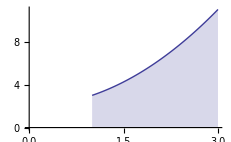

```mathematica
Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Se puede aproximar por la media de los valores en una partición del intervalo. Podemos hacer n subintervalos de anchura Δx.

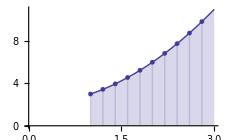

```mathematica
Show[Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis],ListPlot[Table[{1+i/5,(1+i/5)^2+2},{i,0,9}], PlotStyle->PointSize[0.015], Filling->Axis]]
```

Dado que Δx=(b-a)/n tenemos que n=(b-a)/Δx. Por tanto n→∞ cuando Δx→0.
Valor medio =Límite (n→∞)  (∑f(x_i))/n =Límite (Δx→0)  (∑f(x_i))/((b-a)/Δx)=Límite (Δx→0)  (∑f(x_i))/(b-a)Δx = (∫_a^b f(x)ⅆx)/(b-a)

```mathematica
(∫_1^3 (x^2+2) ⅆx)/(3-1)
```

19/3

El valor medio sería la constante bajo cuya gráfica hay la misma área que bajo la gráfica de la función.

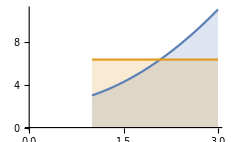

```mathematica
Plot[{x^2+2,19/3},{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

## Área bajo una gráfica

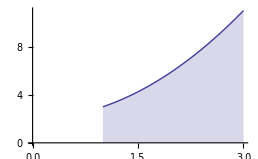

```mathematica
Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Se puede aproximar por la suma de las áreas de los rectángulos.

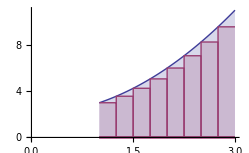

```mathematica
Plot[{x^2+2,Table[Which[ 1+(2i)/8≤x≤1+(2(i+1))/8,(1+2i/8)^2+2,True,0],{i,0,8}]},{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Área =Límite (Δx→0) de las sumas de las áreas de los rectángulos (Base (Δx) por altura (f(x_i)) 
= Límite (Δx→0)  ∑f(x_i) Δx =∫_a^b f(x)ⅆx

```mathematica
∫_1^3 (x^2+2) ⅆx
```

38/3

Volumen obtenido al girar respecto al eje OX una función f(x) ( Método de los discos )

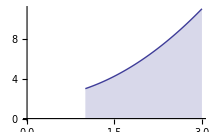

```mathematica
Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Podemos hacer n subintervalos de anchura Δx.

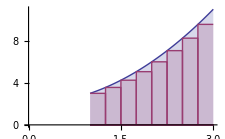

```mathematica
Plot[{x^2+2,Table[Which[ 1+(2i)/8≤x≤1+(2(i+1))/8,(1+2i/8)^2+2,True,0],{i,0,8}]},{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

Ahora podemos girar respecto al eje x y obtenemos discos. El volumen del sólido de revolución se puede aproximar por la suma de los volúmenes de cada uno de los discos.

```mathematica
ParametricPlot3D[{{x,(x^2+2)Cos[t],(x^2+2) Sin[t]},{1,3 Cos[t] (x-1)/2,3Sin[t](x-1)/2},{3,11 Cos[t](x-1)/2,11 Sin[t](x-1)/2}},{x,1,3},{t,0,2Pi}]
```

-Graphics3D-

Se puede aproximar por la suma de los volúmenes de los discos.

```mathematica
ParametricPlot3D[Table[Which[ 1+(2i)/4≤ x≤1+(2(i+1))/4,{x,((1+2i/4)^2+2) Cos[t], ((1+2i/4)^2+2) Sin[t]},True,{x,0,0}],{i,0,4}],{x,1,3},{t,0,2Pi},PlotRange->All,Mesh->{7}]
```

-Graphics3D-

Volumen sólido revolución = Límite (Δx→0) (suma de los volúmenes de los discos(el volumen de cada disco será el área del círculo (π Radio^2 por el grosor Δx) = Límite (Δx→0) ∑π f^2(x_i) Δx =∫_a^b π f^2(x)ⅆx

```mathematica
∫_1^3 π(x^2+2)^2 ⅆx
```

(1366 π)/15

Volumen obtenido al girar respecto al eje OY una función f (x) ( Método de capas )

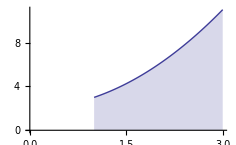

```mathematica
Plot[x^2+2,{x,1,3},AxesOrigin->{0,0}, Filling->Axis]
```

```mathematica
Plot3D[{x^2+y^2+2,0},{x,-3,3},{y,-3,3},RegionFunction->(1<#1^2+#2^2<9&),Filling->Axis,Mesh->None]
```

-Graphics3D-

Se puede aproximar por la suma de los volúmenes de las "capas"

```mathematica
Plot3D[{7,0},{x,-3,3},{y,-3,3},RegionFunction->(4<#1^2+#2^2<5&),Filling->Axis,Mesh->None]
```

-Graphics3D-

Volumen = Límite (Δx→0) (suma de los volúmenes de las capas, que aproximamos por longitud de la circunferencia, por la altura y por el grosor de la capa) ∑2π x f(x) Δx =∫_a^b 2 π x f(x)ⅆx

Observación: Si la capa es muy fina la aproximación anterior se puede admitir. En realidad, el volumen de una capa es igual a la diferencia entre el volumen del cilindro grande menos el volumen del cilindro pequeño (area de la base, π*r^2, por la altura)  π f(x_i) ((x_i+Δx)^2-x_i^2) =  π f(x_i) (2 x_i Δx-Δx^2). Por tanto, sería

Volumen sólido revolución=Límite (Δx→0)  ∑π f(x_i) (2 x_i Δ x-Δ x^2) =Límite (Δx→0)  ∑π f(x_i) (2 x_i-Δx)Δx =∫_a^b π f(x)(2x-0)ⅆx=∫_a^b 2 π x f(x)ⅆx

```mathematica
∫_1^3 2π x (x^2+2)ⅆx
```

56 π

Longitud de una curva, gráfica de una función

Dada una función f (x) = x^2 -3x+3 en un intervalo [1,3], queremos calcular la longitud de esta curva en este intervalo.

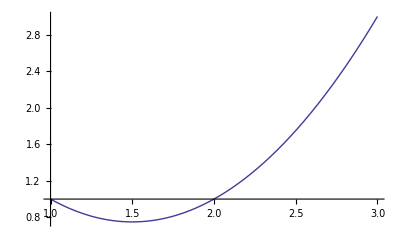

```mathematica
Plot[x^2-3x+3,{x,1,3}]
```

Se puede aproximar por la suma de segmentos.

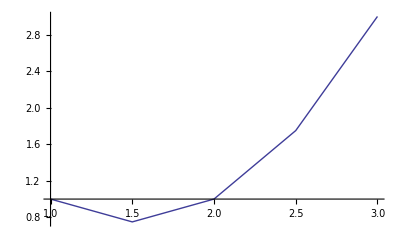

```mathematica
ListPlot[Table[{1+i/2,(1+i/2)^2-3(1+i/2)+3},{i,0,4}],Joined->True]
```

Longitud = Límite (Δx→0) (suma de longitud de cada segmento (hipotenusa de un triángulo rectángulo cuyos catetos son Δ x, Δ f) )=Límite (Δx→0) ∑√(Δ x^2+Δ f^2)=(Multiplicamos y dividimos por  Δ x) =Límite (Δ x→0) ∑√((1+(Δ f^2)/(Δ x^2))Δ x^2)= Límite (Δ x→0) ∑√(1+(Δ f^2)/(Δ x^2))   Δ x  == Límite (Δ x→0) ∑√(1+((Δ f)/(Δ x))^2) Δ x=∫_a^b √(1+f'(x)^2)ⅆx

```mathematica
∫_1^3 √(1+(2x-3)^2)ⅆx
```

1/4 (√2+3 √10+ArcSinh[1]+ArcSinh[3])

```mathematica
N[%]
```

3.40022

Área de una Superficie de revolución, obtenida a partir de una función f(x) al girar sobre el eje x.

```mathematica
Plot[x^2-3x+3,{x,1,3}]
```

-Graphics-

```mathematica
ParametricPlot3D[{x,(x^2-3x+3) Cos[t], (x^2-3x+3) Sin[t]},{x,1,3},{t,0,2π}]
```

-Graphics3D-

Se puede aproximar por la suma de trozos de conos.

```mathematica
Clear[puntos, poligonal,x,t]
```

```mathematica
puntos=Table[(1+i/2)^2-3(1+i/2)+3,{i,0,4}]
```

{1,3/4,1,7/4,3}

```mathematica
poligonal[x_]:=∑_(i=1)^5 (puntos[[i]] Which[1+(i-2)/2≤x≤1+(i-1)/2, 2(x-(1+(i-2)/2)), 1+(i-1)/2≤x≤1+i/2,2((1+i/2)-x),True,0])
```

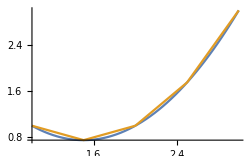

```mathematica
Plot[{x^2-3x+3,poligonal[x]},{x,1,3}]
```

```mathematica
poligonal[x]
```

Which[1/2≤x≤1,2 (x-(1+(i-2)/2)),1+(i-1)/2≤x≤1+i/2,2 ((1+i/2)-x),True,0]+3/4 Which[1≤x≤3/2,2 (x-(1+(i-2)/2)),1+(i-1)/2≤x≤1+i/2,2 ((1+i/2)-x),True,0]+Which[3/2≤x≤2,2 (x-(1+(i-2)/2)),1+(i-1)/2≤x≤1+i/2,2 ((1+i/2)-x),True,0]+7/4 Which[2≤x≤5/2,2 (x-(1+(i-2)/2)),1+(i-1)/2≤x≤1+i/2,2 ((1+i/2)-x),True,0]+3 Which[5/2≤x≤3,2 (x-(1+(i-2)/2)),1+(i-1)/2≤x≤1+i/2,2 ((1+i/2)-x),True,0]

```mathematica
ParametricPlot3D[{x,poligonal[x] Cos[t], poligonal[x] Sin[t]},{x,1,3},{t,0,2π}]
```

ParametricPlot3D::exclul: … must be a list of equalities or real-valued functions.

-Graphics3D-

Área superficie de revolución= Límite (Δx→0) (suma de las áreas de los trozos de conos) ∑π (f(x)+(f(x)+Δf))√(Δ x^2+Δ f^2)= Límite (Δ x→0) ∑π (2f(x)+Δ f)√((1+(Δ f^2)/(Δ x^2))Δ x^2)= Límite (Δ x→0) ∑π (2f(x)+Δ f)√(1+((Δ f)/(Δ x))^2) Δ x  =∫_a^b 2π f(x)√(1+f'(x)^2)ⅆx

```mathematica
∫_1^3 2π (x^2-3x+3)√(1+(2x-3)^2)ⅆx
```

1/32 π (3 √2 (5+31 √5)+11 ArcSinh[1]+11 ArcSinh[3])

```mathematica
N[%]
```

33.8706

## Ejemplo 1

## Cálculo del volumen obtenido al girar la gráfica de una función f(x) respecto al eje y ( Método por capas )

Consideramos la función f(x) = x^2+2 en el intervalo [1,3].

```mathematica
f[x_]:=x^2+2
```

```mathematica
a=1
```

1

```mathematica
b=3
```

3

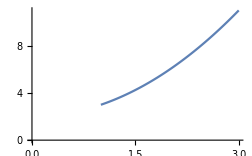

```mathematica
Plot[f[x],{x,a,b},AxesOrigin->{0,0}]
```

Consideremos el área bajo la gráfica

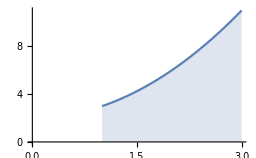

```mathematica
Plot[f[x],{x,a,b},AxesOrigin->{0,0}, Filling->Axis]
```

Consideremos el cuerpo generado al girar esta superficie respecto al eje y.

```mathematica
ParametricPlot3D[{{x Cos[t],x Sin[t],f[x]},{x Cos[t],x Sin[t],0},{a Cos[t],a Sin[t],(f[a])(x-a)/(b-a)},{b Cos[t],b Sin[t],f[b](x-a)/(b-a)}},{x,a,b},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
∫_1^3 2π x f[x]ⅆx
```

56 π

## Ejemplo 2.

## Cálculo del área de una superficie de revolución.

Dada una función f(x) = sen x en el intervalo [0,π], consideramos su gráfica

```mathematica
f[x_]:=Sin[x]
```

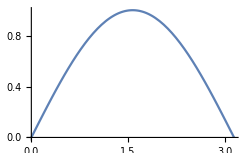

```mathematica
Plot[f[x],{x,0,π}]
```

La superficie de revolución que se obtiene es

```mathematica
ParametricPlot3D[{x,f[x] Cos[t],f[x] Sin[t]},{x,0,π},{t,0,2π}]
```

-Graphics3D-

El área de la superficie exterior viene dada por la integral

```mathematica
∫_0^π 2π f[x] √(1+f'[x]^2)ⅆx
```

2 π (√2+ArcSinh[1])

Este es el área. Si queremos una aproximación numérica usamos la función N.

```mathematica
N[%]
```

14.4236

## Ejemplo 3.

## Valor medio de una función en un intervalo

Dada una función f (x) en un intervalo [a, b], se define el valor medio de f en [a,b] como el valor de la constante que en el intervalo [a,b] tiene la misma integral que f(x). Es decir,

valor medio = (∫_a^b f(x)ⅆx)/(b-a)

```mathematica
f[x_]:=3+x/2+ (2-x)Cos[x^2+2]
```

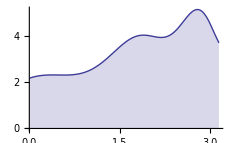

```mathematica
Plot[f[x],{x,0,π},AxesOrigin->{0,0}, Filling->Axis]
```

```mathematica
v=(∫_0^π f[x]ⅆx)/(π-0)
```

1/π(3 π+π^2/4+√(2 π) (Cos[2] FresnelC[√(2 π)]-FresnelS[√(2 π)] Sin[2])+1/2 (Sin[2]-Sin[2+π^2]))

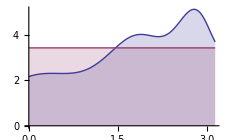

```mathematica
Plot[{f[x],v},{x,0,π},AxesOrigin->{0,0}, Filling->Axis]
```

```mathematica
N[v]
```

3.43512

El valor medio de la función f en el intervalo [0,π] es v (aproximadamente 3.43512). La función constante v, encierra el mismo área que la función f en el intervalo [0,π].

## Integrales impropias

Las integrales definidas que hemos estudiado hasta ahora se correspondían con funciones continuas definidas en intervalos [a,b]. Podemos preguntarnos qué ocurriría si extendemos alguno de los límites del intervalo hacia el infinito, o qué ocurriría si la función no estuviese definida en todo el intervalo [a,b], tendiendo a infinito en alguno de los extremos.

```mathematica
f[x_]:= 1/x^2
```

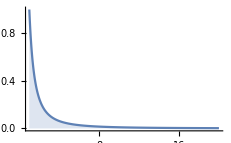

```mathematica
Plot[f[x],{x,1,20},AxesOrigin->{0,0}, Filling->Axis, PlotRange->All]
```

Se podrá calcular el área cuando extendemos el intervalo hacia el 0? y hacia infinito?

## Ejemplo 4

## Cálculo de una integral impropia (intervalo infinito).

Calcular si es posible ∫_1^∞ f(x)ⅆx. Para ello calculamos la integral en [1,b] y luego hacemos tender b a infinito.

```mathematica
f[x_]:= 1/x^2
```

```mathematica
∫_1^b f[x]ⅆx
```

ConditionalExpression[1-1/b, Re[b]>0||b∉ℝ]

```mathematica
Limit[∫_1^b f[x]ⅆx,b->Infinity]
```

1

Vemos que el límite existe y será el valor de la integral impropia ∫_1^∞ f(x)ⅆx.

## Ejemplo 5

## Cálculo del área bajo una gráfica en un intervalo de longitud infinita. ( f(x)=1/x, en el intervalo [1,+∞) )

Veamos ahora otro ejemplo:

```mathematica
f[x_]:=1/x
```

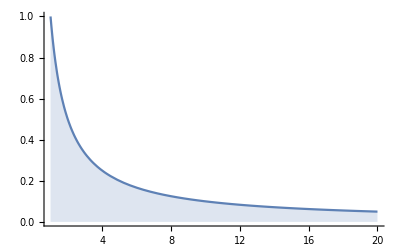

```mathematica
Plot[f[x],{x,1,20},AxesOrigin->{0,0}, Filling->Axis, PlotRange->All]
```

```mathematica
Limit[∫_1^b f[x]ⅆx,b->Infinity]
```

∞

```mathematica
∫_1^∞ f[x]ⅆx
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

∫_1^∞ 1/x ⅆx

El área bajo la gráfica tiende a infinito. Podríamos decir que la integral impropia no converge o que tiende a infinito.

## Ejemplo 6

## Cálculo del volumen obtenido al girar respecto al eje OX una gráfica en un intervalo de longitud infinita. ( f(x)=1/x, en el intervalo [1,+∞) )

Continuamos con el ejemplo anterior.

```mathematica
f[x_]:=1/x
```

```mathematica
ParametricPlot3D[{x,f[x] Cos[t], f[x] Sin[t]},{t,0,2Pi},{x,1,20}, PlotRange->All]
```

-Graphics3D-

```mathematica
Volumen=Limit[∫_1^b π f[x]^2 ⅆx,b->Infinity]
```

π

El volumen del sólido de revolución tiende a π.

## Ejemplo 7

## Cálculo de la superficie de un sólido de revolución obtenido al girar respecto al eje OX una gráfica en un intervalo de longitud infinita. ( f(x)=1/x, en el intervalo [1,+∞) )

Continuamos con el ejemplo anterior.

```mathematica
f[x_]:=1/x
```

```mathematica
∫2 π f[x] √(1+f'[x]^2)ⅆx
```

2 π (-1/2 √(1+1/x^4)+(√(1+1/x^4) x^2 ArcTanh[x^2/(√(1+x^4))])/(2 √(1+x^4)))

```mathematica
2 π (-1/2 √(1+1/x^4)+(√(1+1/x^4) x^2 ArcTanh[x^2/(√(1+x^4))])/(2 √(1+x^4)))/.x->1
```

2 π (-1/(√2)+1/2 ArcTanh[1/(√2)])

```mathematica
2 π (-1/2 √(1+1/x^4)+(√(1+1/x^4) x^2 ArcTanh[x^2/(√(1+x^4))])/(2 √(1+x^4)))/.x-> b
```

2 π (-1/2 √(1+1/b^4)+(√(1+1/b^4) b^2 ArcTanh[b^2/(√(1+b^4))])/(2 √(1+b^4)))

```mathematica
Limit[2 π (-1/2 √(1+1/b^4)+(√(1+1/b^4) b^2 ArcTanh[b^2/(√(1+b^4))])/(2 √(1+b^4))),b->Infinity]
```

∞

El área de la superficie de revolución tiende a infinito. 
Observemos que el volumen dentro de la superficie de revolución es finito, sin embargo el área es infinita.

## Ejemplo 8

## Cálculo del volumen obtenido al girar respecto al eje OY una gráfica en un intervalo de longitud infinita.

Continuamos con el ejemplo anterior aunque ahora giramos respecto al eje y.

```mathematica
f[x_]:=1/x
```

```mathematica
ParametricPlot3D[{{x Cos[t],x Sin[t], f[x]},{x Cos[t],x Sin[t],0}},{x,1,20},{t,0,2Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
volumencapas=Limit[∫_1^b 2π x f[x]ⅆx,b->Infinity]
```

∞

El volumen de esta superficie de revolución tiende a infinito.

## Ejemplo 9

## Cálculo de una integral impropia (intervalo finito). (Área, volumen al girar respecto al eje x, superficie del sólido de revolución, volumen al girar respecto al eje y)

Otro ejemplo de integral impropia, ahora porque la función tiende a infinito cuando la variable se acerca al extremo del intervalo.
Calcular ∫_1^2 1/(√(x - 1))ⅆx

```mathematica
g[x_]:=1/(√(x-1))
```

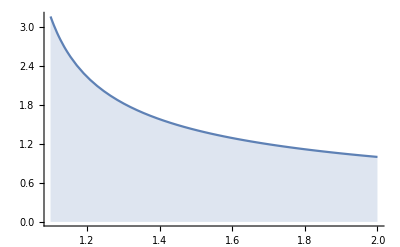

```mathematica
Plot[g[x],{x,1.1,2},AxesOrigin->{0,0}, Filling->Axis, PlotRange->All]
```

Podemos calcular la primitiva

```mathematica
∫g[x]ⅆx
```

2 √(-1+x)

```mathematica
h[x_]:=2 √(-1+x)
```

Calculamos la diferencia entre el valor en 2 y en a, y calculamos el límite.

```mathematica
Limit[h[2]-h[a],a->1]
```

2

También podemos calcular la integral definida

```mathematica
∫_a^2 g[x]ⅆx
```

ConditionalExpression[2-2 √(-1+a), ]

y hacer el límite

```mathematica
area=Limit[∫_a^2 g[x]ⅆx, a->1,Direction->-1]
```

2

O directamente escribir la integral impropia

```mathematica
∫_1^2 g[x]ⅆx
```

2

El área bajo la curva es finita y tiende a 2.

```mathematica
ParametricPlot3D[{x,g[x] Cos[t], g[x] Sin[t]},{t,0,2Pi},{x,1.1,2}, PlotRange->All]
```

-Graphics3D-

```mathematica
Volumen=Limit[∫_a^2 π g[x]^2 ⅆx,a->1]
```

∞

El volumen del sólido obtenido al girar respecto el eje x,en cambio tiende a infinito.

```mathematica
Area=Limit[∫_a^2 2 π g[x] √(1+g'[x]^2)ⅆx,a->1]
```

∞

El área de la superficie de revolución obtenido al girar respecto el eje x, tiende a infinito.

```mathematica
∫_1.1^2 2 π g[x] √(1+g'[x]^2)ⅆx
```

30.7432-9.11417×10^-15 ⅈ

```mathematica
ParametricPlot3D[{{x Cos[t],x Sin[t], g[x]},{x Cos[t],x Sin[t],0},{Cos[t],Sin[t],3x-3.3}, {2 Cos[t],2 Sin[t], x-1.1}},{x,1.1,2},{t,0,2Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
volumencapas=Limit[∫_a^2 2π x g[x]ⅆx,a->1]
```

(16 π)/3

En cambio, el volumen de la superficie de revolución al girar respecto a eje y es finito.

## Más ejemplos

Calcular el volumen/área de la superficie obtenida el girar la gráfica de la función √(1+x)-1 con x en [0,2] alrededor del eje horizontal.

```mathematica
f[x_]:= Sqrt[1+x]-1
```

```mathematica
Plot[f[x],{x,0,2}]
```

-Graphics-

```mathematica
ParametricPlot3D[{x,f[x] Cos[t],f[x] Sin[t]},{x,0,2},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
∫_0^2 π (f[x])^2ⅆx
```

(22/3-4 √3) π

```mathematica
∫_0^2 2π f[x] √(1+f'[x]^2)ⅆx
```

1/6 π (√5+13 √13-6 √39+3 ArcSinh[2]-3 ArcSinh[2 √3])

Volumen del toro de radio grande 5 y radio pequeño 2 (como diferencia de volúmenes de revolución obtenidos al girar dos semicircunferencias)

```mathematica
Clear[R,r]
```

```mathematica
R=5;
```

```mathematica
r=2;
```

```mathematica
f[x_]:= R+Sqrt[r^2-x^2]
```

```mathematica
g[x_]:=R-Sqrt[r^2-x^2]
```

```mathematica
ParametricPlot3D[{{x,f[x] Cos[t],f[x] Sin[t]},{x,g[x] Cos[t],g[x] Sin[t]}},{x,-r,r},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
{ParametricPlot3D[{{x,f[x] Cos[t],f[x] Sin[t]},{-r,R Cos[t] (x+r)/(2r),R Sin[t](x+r)/(2r)},{r,R Cos[t](x+r)/(2r),R Sin[t](x+r)/(2r)}},{x,-r,r},{t,0,2Pi}],ParametricPlot3D[{{x,g[x] Cos[t],g[x] Sin[t]},{-r,R Cos[t] (x+r)/(2r),R Sin[t](x+r)/(2r)},{r,R Cos[t](x+r)/(2r),R Sin[t](x+r)/(2r)}},{x,-r,r},{t,0,2Pi}]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
∫_-r^r π (f[x])^2ⅆx-∫_-r^r π (g[x])^2ⅆx//Simplify
```

40 π^2

Calcular el volumen del cono obtenido al girar la gráfica de la función 4-2x en el intervalo [0,2] respecto al eje vertical.

```mathematica
f[x_]:=4-2x
```

```mathematica
a=0;
```

```mathematica
b=2;
```

```mathematica
ParametricPlot3D[{{x Cos[t],x Sin[t],f[x]},{x Cos[t],x Sin[t],0},{a Cos[t],a Sin[t],(f[a])(x-a)/(b-a)},{b Cos[t],b Sin[t],f[b](x-a)/(b-a)}},{x,a,b},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
∫_a^b 2π x f[x]ⅆx
```

(16 π)/3

```mathematica
N[(16 π)/3,40]
```

16.75516081914556393846743137749068204905

Calcular la superficie de la esfera obtenida al girar una función alrededor del eje horizontal.

Como los puntos de la circunferencia centrada en el (0,0) y radio 1 cumplen que x^2+y^2=1, despejamos y como función de x. Aparecerían dos funciones y=√(1-x^2), y=-√(1-x^2). La primera tendría como gráfica la semicircunferencia por encima del eje horizontal y la segunda es la que tiene como gráfica la semicircunferencia de abajo. Tomamos la primera función y la hacemos girar respecto al eje horizontal.

```mathematica
f[x_]:= Sqrt[1-x^2]
```

```mathematica
a=-1;
```

```mathematica
b=1;
```

```mathematica
ParametricPlot3D[{x, f[x] Cos[t],f[x] Sin[t]},{t,0,2Pi},{x,a,b}]
```

-Graphics3D-

La fórmula para calcular la superficie es ∫_a^b 2 π f[x] √(1+f'[x]^2)ⅆx

```mathematica
∫_a^b 2π f[x] √(1+f'[x]^2)ⅆx
```

4 π

```mathematica
N[%]
```

33.8706